√(16-x^2)

4 π

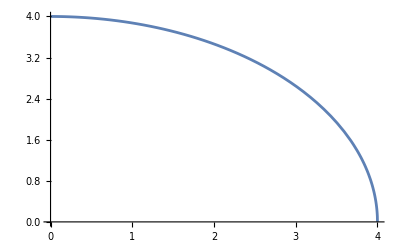

```mathematica
g = Sqrt[16-x^2]
Integrate[g, {x,0,4}]
Plot[g, {x,0,4}]
```

√(25-(-5+x)^2)

{x,0,10}

(25 π)/2

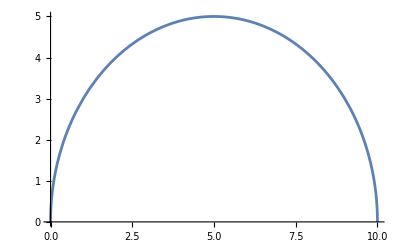

```mathematica
g = Sqrt[25-(x-5)^2]
bounds={x,0,10}
Integrate[g, bounds]
Plot[g, bounds]
```

Abs[-4+x]

{x,0,6}

10

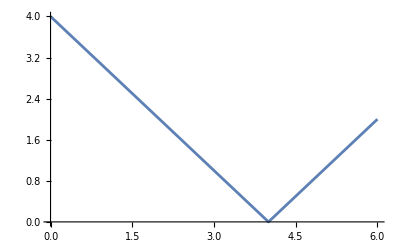

```mathematica
g = Abs[x-4]
bounds={x,0,6}
Integrate[g, bounds]
Plot[g, bounds]
```

Piecewise[{{2, 0<x<5}, {0, True}}]

{x,-∞,∞}

10

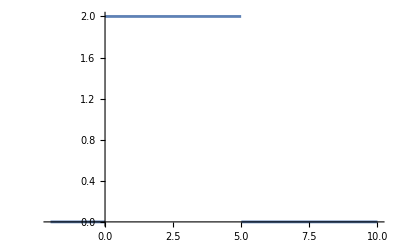

```mathematica
g = Piecewise[{{2,0<x<5}}]
bounds={x,-Infinity,Infinity}
Integrate[g,bounds]
```

```mathematica
g = Piecewise[{{1,-2<x<10}}]
bounds={x,-Infinity,Infinity}
A=Integrate[g,bounds]
k=1/A
```

Piecewise[{{1, -2<x<10}, {0, True}}]

{x,-∞,∞}

12

1/12

```mathematica
g = Piecewise[{{x^2+x,0<x<1}}];
bounds={x,-Infinity,Infinity};
A=Integrate[g,bounds];
k=1/A
f=k*g
Integrate[f,bounds]==1;
EV = Integrate[x f,bounds]
Var = Integrate[(x-EV)^2*f,bounds]
```

6/5

6/5 (Piecewise[{{x+x^2, 0<x<1}, {0, True}}])

7/10

1/20

```mathematica
g = Piecewise[{{3x^2,0<x<1}}];
bounds={x,-Infinity,Infinity};
A=Integrate[g,bounds];
k=1/A;
f=k*g;
Integrate[f,bounds]==1;
EV = Integrate[x f,bounds];
Var = Integrate[(x-EV)^2*f,bounds];
{A,EV,Var}
%//N
```

{1,3/4,3/80}

{1.,0.75,0.0375}

```mathematica
$Assumptions=x∈Reals
g = Piecewise[{{1,-2<x<10}}];
bounds={x,-Infinity,Infinity};
A=Integrate[g,bounds];
k=1/A;
f=k*g;
Integrate[f,bounds]==1;
EV = Integrate[x f,bounds];
Var = Integrate[(x-EV)^2*f,bounds];
{A,EV,Var}
%//N
F = Integrate[f,{x,-Infinity,x}]
f
D[F,x]
```

x∈ℝ

{12,4,12}

{12.,4.,12.}

Piecewise[{{1, x>10}, {(2+x)/12, -2<x≤10}, {0, True}}]

1/12 (Piecewise[{{1, -2<x<10}, {0, True}}])

Piecewise[{{0, x<-2}, {1/12, -2<x<10}, {0, x>10}, {Indeterminate, True}}]

```mathematica
$Assumptions=x∈Reals&& a<b;
g = Piecewise[{{1,a<x<b}}];
bounds={x,-Infinity,Infinity};
A=Integrate[g,bounds];
k=1/A;
f=k*g;
Integrate[f,bounds]==1;
EV = Integrate[x f,bounds];
Var = Integrate[(x-EV)^2*f,bounds];
{EV,Var}
Quit[]
```

{(a+b)/2,1/12 (a-b)^2}

```mathematica
g = Piecewise[{{3,-2<x<1},{5,1<x<5}}];
Plot[g,{x,-10,10}];
bounds={x,-Infinity,Infinity}
A=Integrate[g,bounds]
k=1/A;
f=k g;
EV = Integrate[x f,bounds];
Var = Integrate[(x-EV)^2*f,bounds];
{EV,Var}
%//N
```

{x,-∞,∞}

29

{111/58,38089/10092}

{1.91379,3.77418}